# Poisson problem - High gradient with Arc Tan

## Global variables

```mathematica
(*Clear[KValue]
KValue=10000;*)
Clear[F]
F[Kv_]:= 2Sqrt[Kv];
```

## One dimensional problem - Solution

```mathematica
Clear[a,r,P]
r=0.25;
a=0.5;
P=2./Pi;
Coeff = -2.;
arc[x_,Kv_]:= F[Kv]*(r^2- (x-a)*(x-a));
prodx[x_]:=x*(x-1.);
Sol1D[x_,Kv_]:=Coeff*prodx[x]*(1.+P*ArcTan[arc[x,Kv]])
```

```mathematica
DSol1D[x_,Kv_]:=Simplify[D[Sol1D[x,Kv],x]]
```

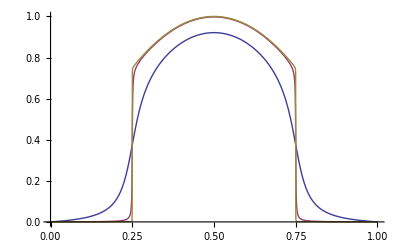

```mathematica
Plot[{Sol1D[x,1000],Sol1D[x,1000000],Sol1D[x,1000000000]},{x,0,1.},AxesOrigin->{0.,0.}]
```

```mathematica
Coeff = 8.;
arc[x_,y_,Kv_]:= F[Kv]*((0.25)^2 - (x-0.5)^2- (y-0.5)^2);
prod[x_]:=x*(x-1.);
Sol2D[x_,y_,Kv_]:=Coeff*prod[x]*prod[y]*(1.+(2./Pi)*ArcTan[arc[x,y,Kv]])
```

```mathematica
Plot3D[Sol2D[x,y,1000000],{x,0.,1.},{y,0.,1.}]
```

-Graphics3D-

## Three Dimensional problem - Solution

```mathematica
Clear[arc,prod,Coeff]
Coeff = -32.;
arc[x_,y_,z_,Kv_]:= F[Kv]*((0.25)^2 - (x-0.5)^2- (y-0.5)^2- (z-0.5)^2);
prod[x_]:=x*(x-1.);
Sol3D[x_,y_,z_,Kv_]:=Coeff*prod[x]*prod[y]*prod[z]*(1.+(2./Pi)*ArcTan[arc[x,y,z,Kv]])
```

```mathematica
RegionPlot3D[Sol3D[x,y,z,1000000]>.9,{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
u[x_,y_]:=0.5*Power[Sqrt[x*x+y*y],(1./3.)]*(Sqrt[3]*Sin[ArcTan[x,y]/3]+Cos[ArcTan[x,y]/3.])
```

```mathematica
Plot3D[u[x,y],{x,-1,1},{y,0,1}]
Plot3D[u[x,y],{x,0,1},{y,-1,0}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ClearAll[x,y]
u1[x_,y_]:=Sqrt[x^2+y^2]^(1/3) Sin[1/3(ArcTan[x,y]+Pi/2)]
a=Plot3D[u1[x,y],{x,-1,1},{y,0,1}]
b=Plot3D[u1[x,y],{x,0,1},{y,-1,1}]
Show[a,b,PlotRange->{{-1,1},{-1,1}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## ERROR TABLES

## 2013/10/17

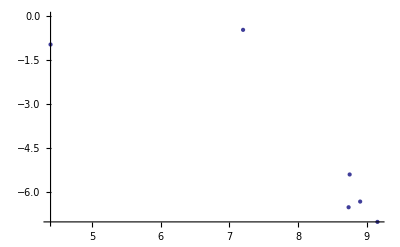

```mathematica
NEqs={81,1337,6313,7357,9465,6217};
Errors={0.382899,0.63239,0.00447946,0.00177273,0.000883817,0.0014585};
LNeqs=Table[Log[NEqs[[i]]],{i,1,Length[NEqs]}];
LErrors=Table[Log[Errors[[i]]],{i,1,Length[Errors]}];
ListPlot[Table[{LNeqs[[i]],LErrors[[i]]},{i,1,Length[LNeqs]}]]
```